```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/github_public_repos/d-Cubic/examples/test_interp_1d

Grid

```mathematica
grid=Import["test_interp_1d.txt","Table"];
```

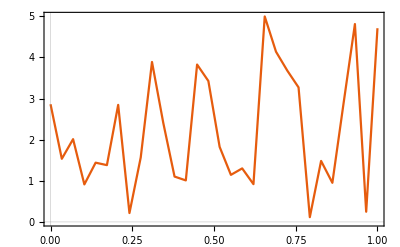

```mathematica
ListLinePlot[grid]
```

```mathematica
xSpacing=Abs[grid[[2,1]]-grid[[1,1]]]
```

0.0344828

Analytic formula

```mathematica
cubic[p0_,p1_,p2_,p3_,x_]:=(-0.5*p0+1.5*p1-1.5*p2+0.5*p3)*x^3+(p0-2.5*p1+2.0*p2-0.5*p3)*x^2+(-0.5*p0+0.5*p2)*x+p1;
```

Test point

```mathematica
xTest=0.71;
```

Convert to fraction

```mathematica
pt1=Select[grid,#[[1]]>xTest-xSpacing&&#[[1]]<xTest&][[1]]
```

{0.689655,4.13986}

```mathematica
xFrac=(xTest-pt1[[1]])/xSpacing
```

0.590004

Make p values

```mathematica
p=Association[];
Do[
p[i]=Select[grid,#[[1]]>xTest+(i-2)*xSpacing&&#[[1]]<xTest+(i-1)*xSpacing&][[1,2]];
,{i,0,3}];
```

```mathematica
p
```

<|0→4.99727,1→4.13986,2→3.68051,3→3.27156|>

Evaluate test

```mathematica
cubic[p[0],p[1],p[2],p[3],xFrac]
```

3.84551